```mathematica
Quiet@Remove@"`*";ClearAll@"`*";
On[Assert]
SetDirectory[NotebookDirectory[]];

Row@{"Suffix: ",suffix="hT"}
theoryData=Import[StringJoin["theory-",suffix,".json"], "RawJSON"]
mcData=Import[StringJoin["mc-",suffix,".json"], "RawJSON"];
a1Data=Import[StringJoin["a1-",suffix,".json"], "RawJSON"];
a2Data=Import[StringJoin["a2-",suffix,".json"], "RawJSON"];
```

Suffix: hT

<|coupling→-1,temperature→2,field→0.4,number of spins→10,energy_level→{-10.,-6.8,-6.8,-6.8,-6.,-6.,-6.,-5.2,-5.2,-3.6,-3.6,-3.6,-2.8,-2.8,-2.8,-2.,-2.,-2.,-2.,-1.2,-1.2,-1.2,-1.2,-0.4,-0.4,-0.4,-0.4,-0.4,-0.4,-0.4,-0.4,0.4,0.4,0.4,0.4,0.4,0.4,1.2,1.2,1.2,2.,2.,2.,2.,2.8,2.8,2.8,2.8,2.8,3.6,3.6,3.6,3.6,4.4,4.4,5.2,5.2,5.2,6.,6.,6.,6.8,6.8,7.6,7.6,8.4,9.2,14.},magnetization_level→{-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.},energy_probs→{0.0809783,0.0899208,0.0163492,0.0980955,0.191786,0.0164388,0.0109592,0.0146924,0.077135,0.00165043,0.0412607,0.0396103,0.0132758,0.0918241,0.00553157,0.00444951,0.0682258,0.00444951,0.0118654,0.000497099,0.0303231,0.0024855,0.0164043,0.00166608,0.0043318,0.00666431,0.0043318,0.00333216,0.00399859,0.00366537,0.000333216,0.000670083,0.00670083,0.00379714,0.00111681,0.000670083,0.000446722,0.00389281,0.00329392,0.00404253,0.00140508,0.000200725,0.00632284,0.000100363,0.0000672751,0.000336375,0.00417105,0.0010764,0.0000672751,0.000135287,0.00184893,0.0011274,0.0000450958,0.000483658,0.00087663,0.0000202629,0.00014184,0.0000405257,0.0000407478,0.0000407478,0.000067913,0.0000637328,0.0000273141,0.0000549275,6.10306×10^-6,0.00004091,0.0000274228,2.48774×10^-7},magnetization_probs→{2.48774×10^-7,0.0000274228,0.00109891,0.0194276,0.146674,0.397318,0.326429,0.0962253,0.0121135,0.000672751,0.0000135826}|>

Sample sizes: 10000

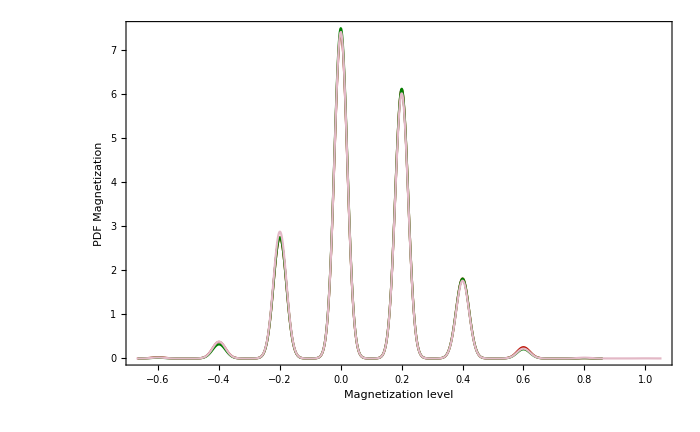

```mathematica
{engyMc,engyA1,engyA2} =#["magnetization_sample"] &/@{mcData,a1Data,a2Data};


Row@{"Sample sizes: ",sampleSize=Length[engyMc]}
Assert@And[
sampleSize==Length[engyA1],
sampleSize==Length[engyA2]
]

engyTheory =Association@MapThread[
Rule[#1,#2]&,{theoryData["magnetization_level"],sampleSize*theoryData["magnetization_probs"]}
];


colors = Table[ColorData[58][i],{i,6}];
baseStyle = Directive[Black, FontFamily->"Arial", FontSize->16];
frameStyle = Append[baseStyle, Thickness@0.003];


mc = SmoothHistogram[engyMc,Automatic, "PDF", PlotRange->All,PlotStyle-> colors[[1]],Axes->False];
a1 = SmoothHistogram[engyA1,Automatic, "PDF", PlotRange->All,PlotStyle-> colors[[2]],Axes->False];
a2 = SmoothHistogram[engyA2,Automatic, "PDF", PlotRange->All,PlotStyle-> colors[[3]],Axes->False];
Show[
{mc, a1, a2},
Epilog->{
Inset[Framed[
SwatchLegend[
Directive[EdgeForm@None,FaceForm@#]&/@colors,
{"MC","DT","CT"},
LegendLayout->"Row",LabelStyle->baseStyle
],FrameStyle->Append[baseStyle,Thickness@1],RoundingRadius->5
],Scaled@{0.7,0.9}]
},
Frame->{{True,True},{True,True}},
FrameStyle->{{Append[baseStyle,Thickness@0.004],Append[baseStyle,Thickness@0.004]},{Append[baseStyle,Thickness@0.004],Append[baseStyle,Thickness@0.004]}},
FrameLabel->{{"PDF Magnetization",""},{"Magnetization level",""}}, 
ImageSize->700
]
```

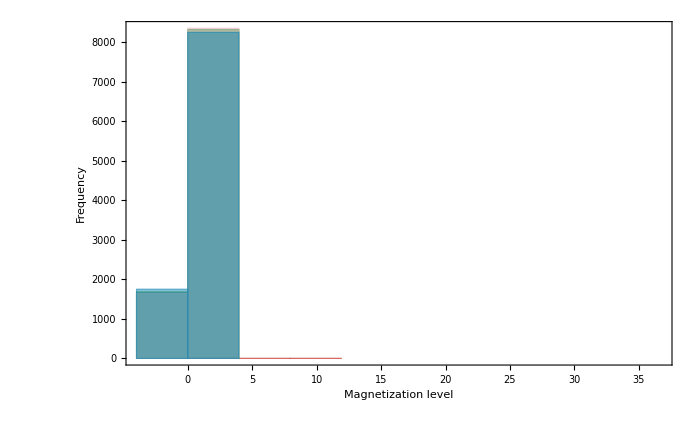

```mathematica
Show[
Histogram[{engyTheory,engyMc, engyA1, engyA2}, ChartStyle->colors],
Epilog->{
Inset[Framed[
SwatchLegend[
Directive[EdgeForm@None,FaceForm@#]&/@colors,
{"Theory","MC","DT","CT"},
LegendLayout->"Row",LabelStyle->baseStyle
],FrameStyle->Append[baseStyle,Thickness@1],RoundingRadius->5
],Scaled@{0.7,0.9}]
},
Frame->{{True,False},{True,False}},
FrameStyle->{{Append[baseStyle,Thickness@0.004],Append[baseStyle,Thickness@0.004]},{Append[baseStyle,Thickness@0.004],Append[baseStyle,Thickness@0.004]}},
FrameLabel->{{"Frequency",""},{"Magnetization level",""}} ,
ImageSize->700
]
```